```mathematica
Exit[]
```

# Gamma qg

```mathematica
<<"/Users/giacomomagni/Documents/Wolfram Mathematica/Sigma.m"
<<"/Users/giacomomagni/Documents/Wolfram Mathematica/HarmonicSums.m"
LaunchKernels[4];
```

Sigma - A summation package by Carsten Schneider — © RISC —  V 2.86 (June 15, 2021)  Help

HarmonicSums by Jakob Ablinger — © RISC — Version 1.0(30/03/21)Help

#### Inputs

```mathematica
here = NotebookDirectory[];
Get[StringJoin[here, "constants.m"]]
```

```mathematica
(* Singlet, large nf exact parts *)
Get[StringJoin[here, "singlet_nf3.m"]]
Get[StringJoin[here, "ns_nf3_nf2.m"]]
(* Singlet, asymptotic N-> Infinity, large nc limit *)
Get[StringJoin[here, "qcd_cusp.m"]]
(* Singlet, moments *)
Get[StringJoin[here, "gqq3nsp.m"]]
Get[StringJoin[here, "gqq3ps.m"]]
Get[StringJoin[here, "gqg3.m"]]
Get[StringJoin[here, "gqg3.m"]]
Get[StringJoin[here, "ggg3.m"]]
```

```mathematica
Get[StringJoin[here, "fitting_utils.m"]]
Get[StringJoin[here, "plotting_utils.m"]]
Get[StringJoin[here, "saving_utils.m"]]
```

### Fitting 4 moments

```mathematica
gqg3N1asy
```

(77.9362 ca (237.458 nf+1. nf^2))/(cf (-1+n)^2)-(256 ca^3 nf (82/81+2 z3))/(3 (-1+n)^3)

Here we add the NLL contribution from qq PS which is determined from 10 moments....

```mathematica
gqg3N1asyExtened = gqg3N1asy + (77.93619924402574 (237.45793768976418 nf+1. nf^2))/(n-1)^2 ca/cf;
```

```mathematica
thrhigh = 10^-7;
thrlow = 10^-3;
gqgmoments = {gqg3N2,gqg3N4,gqg3N6,gqg3N8};

fsmallN = {1/(n-1), 1/(n-1), 1/(n-1)};
flargeN = {S13m1[n],S13m1[n],S13m1[n]};

fSubLeadingLargeN = {
	{1/(n+1),1/(n+1),1/(n+1)},
	{1/(n+2),1/(n+2),1/(n+2)}, 
	{1/(n+1)^2,1/(n+1)^2,1/(n+1)^2}, 
	{1/(n+1)^3,1/(n+1)^3,1/(n+1)^3},
	{Lm11[n],Lm11[n], Lm11[n]}, 
	{Lm12[n],Lm12[n], Lm12[n]}, 
	{Lm13[n],Lm13[n], Lm13[n]},
	{S12m1[n],S12m1[n],S12m1[n]},
	{S[1,n-2]/n,S[1,n-2]/n,S[1,n-2]/n}
};
fSubLeadingSmallN = {
	(* {1/(n-1),1/(n-1),1/n},*)
	{1/n^4,1/n^4,1/n^4},
	{1/n^3,1/n^3,1/n^3},
	{1/n^2,1/n^2,1/n^2},
	{1/n,1/n,1/n}
};

gqg3asy = MellinInverseSinglet[gqg3N0asy + gqg3N1asyExtened + gqg3Ninf] /. Delta[x__] -> 0 /. LimitRules /. ZetaRules;
```

#### Cross candidates

Smooth candidates: 76 out of 78

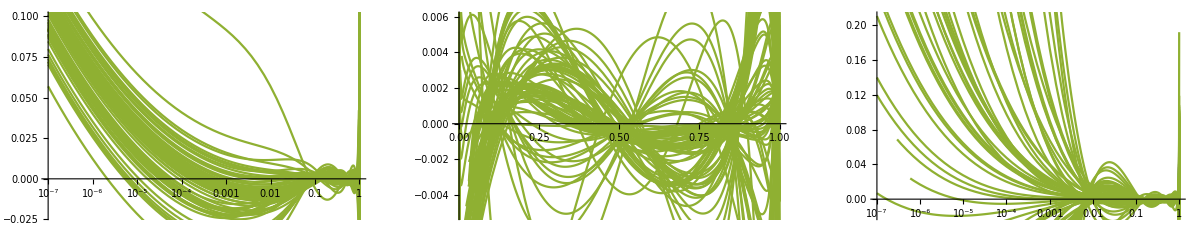

```mathematica
fSubLeadingtot = Join[fSubLeadingSmallN, fSubLeadingLargeN];
gqg3FittedCross = DoAllFits[fsmallN, flargeN, fSubLeadingtot, gqgmoments, gqg3N0asy, gqg3N1asyExtened, gqg3Ninf];
gqg3invfull = ListMellinInverse[gqg3FittedCross];
gqg3inv = SelectSmoothCandidates[gqg3invfull, 4,thrlow,thrlow];
graphQGrep = PlotList[gqg3inv, gqg3asy, 4, 3] // Show;
graphQGlogrep = LogPlotList[gqg3inv, gqg3asy, 4, 3] // Show;
graphQGloglargerep = LogPlotListLargeX[gqg3inv, gqg3asy, 4, 3] // Show;
GraphicsRow[{graphQGlogrep,graphQGrep, graphQGloglargerep}]
```

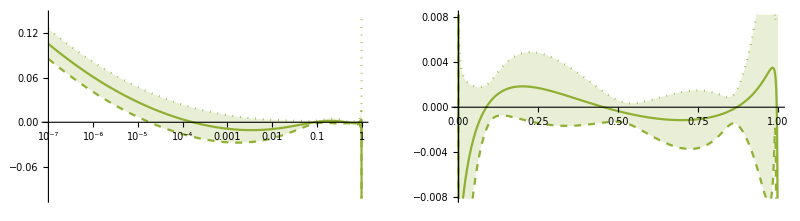

```mathematica
{graphQG,graphQGlog} =  PlotErrorBand[gqg3asy, gqg3inv, 4, 3];
GraphicsRow[{graphQGlog,graphQG}]
```

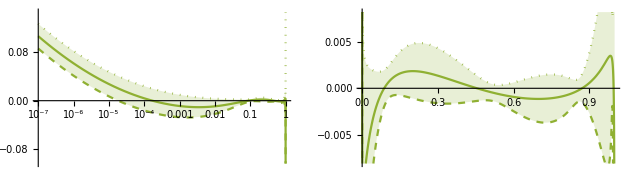

```mathematica
ddd
```

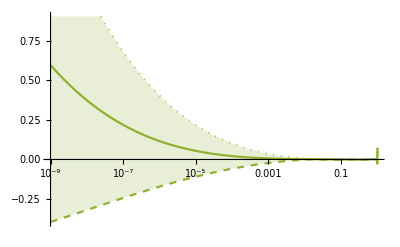

```mathematica
PlotErrorBandLargeX[gqg3asy, gqg3inv, 4, 3]
```

#### Cherry Picking

```mathematica
cherryfunctions = {1/n^3, Lm13[n]};
gqg3cherry = SelectCherriesSpecial[gqg3FittedCross, cherryfunctions];
gqg3cherry = SelectSmoothCandidates[gqg3cherry, 4, thrlow, thrhigh];
```

Selected cherries are: 23 out of 78

Smooth candidates: 20 out of 23

```mathematica
{graphQGcherry, graphQGcherrylog} = PlotErrorBand[gqg3asy, gqg3cherry, 4, 4]; 
legend = {"cross candidate", "cherries"}; 
GraphicsRow[{
    	ShowLegends[{graphQGlog, graphQGcherrylog}, LogLinearPlot, legend, {3, 4}], 
    	ShowLegends[{graphQG, graphQGcherry}, Plot, legend, {3, 4}]
    	}, ImageSize -> Full
 ]
```

-Graphics-

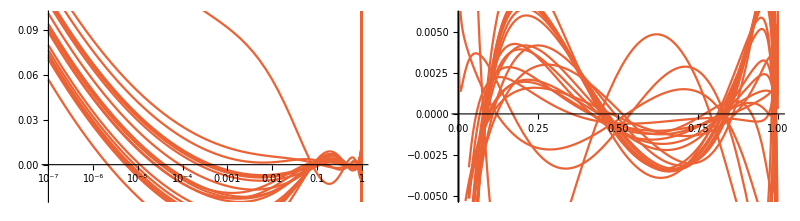

```mathematica
graphQGcherrylogrep = LogPlotList[gqg3cherry, gqg3asy, 4, 4];
graphQGcherryrep = PlotList[gqg3cherry, gqg3asy, 4, 4];
GraphicsRow[{Show[graphQGcherrylogrep], Show[graphQGcherryrep]}]
```

#### Plot nf^3

```mathematica
gqg3asy3 = Coefficient[gqg3asy, nf, 3];
gqg3inv3 =  SelectSmoothCandidates[Coefficient[gqg3inv, nf, 3], 4,thrlow,thrlow];
gqg3inv3cherries =  SelectSmoothCandidates[Coefficient[gqg3cherry, nf, 3], 4,thrlow,thrlow];
gqg3nf3x = gqg3nf3x /. QCDConstantsRules //N;
```

Smooth candidates: 68 out of 76

Smooth candidates: 17 out of 20

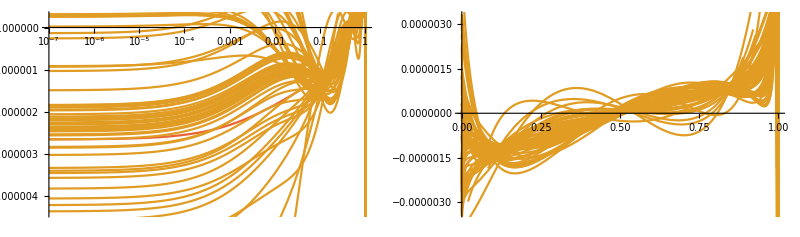

```mathematica
gtmp = PlotList[gqg3inv3, gqg3asy3, 4, 2];
gtmplog = LogPlotList[gqg3inv3, gqg3asy3, 4, 2];
graphQGExa3 = Plot[pifact gqg3nf3x, {x, 0, 1}, PlotStyle -> clist[[4]], ImageSize->Full];
graphQGExa3log = LogLinearPlot[ pifact gqg3nf3x, {x, 10^-7, 1}, PlotStyle -> clist[[4]], ImageSize->Full];
GraphicsRow[{Show[{graphQGExa3log, gtmplog}], Show[{graphQGExa3, gtmp}]}, ImageSize->Full]
```

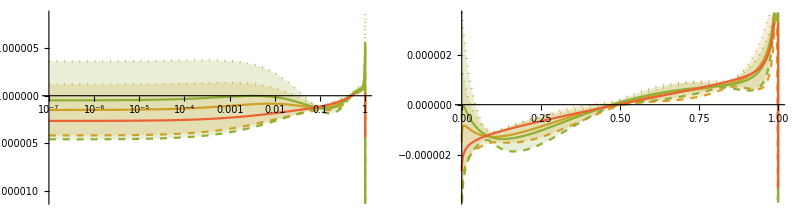

```mathematica
{graphQG3, graphQG3log} = PlotErrorBand[gqg3asy3, gqg3inv3, 4,2];
{graphQG3cherry, graphQG3cherrylog} = PlotErrorBand[gqg3asy3, gqg3inv3cherries, 4,3];
GraphicsRow[{
	Show[graphQG3log, graphQG3cherrylog, graphQGExa3log], 
	Show[graphQG3, graphQG3cherry, graphQGExa3]
	}, ImageSize -> Full
]
```

#### Interpolation checks

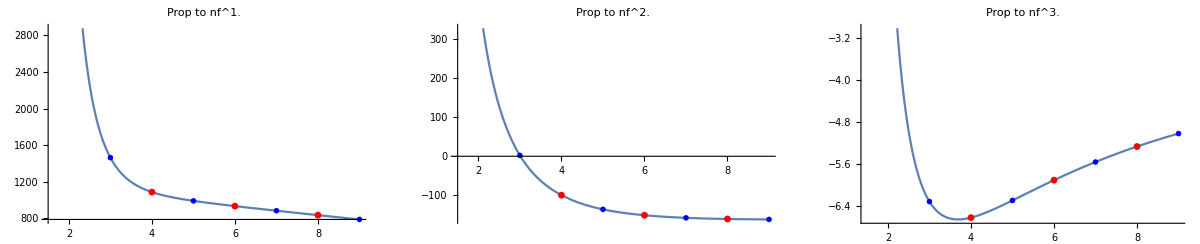

```mathematica
gqg3asytmp = gqg3N0asy+ gqg3N1asyExtened + gqg3Ninf;
GraphicsRow[
	{PlotInterpolation[gqgmoments -gqg3asytmp, {1.1,3,5,7,9}, 1], PlotInterpolation[gqgmoments - gqg3asytmp, {1.5, 3,5,7,9}, 2], PlotInterpolation[gqgmoments -gqg3asytmp, {1.5,3,5,7,9}, 3]}
	, ImageSize->Full, PlotRange->All]
```

```mathematica
ref = gqg3nf3 - Coefficient[gqg3asytmp, nf, 3];
interpolator = MomentListInterpolator[gqgmoments-gqg3asytmp,{2,4,6,8},3] //Simplify ;
Table[
	Print["N: ",n, " Relative err (%): ",(ref - interpolator)/ ref * 100 //. QCDConstantsRules /. ZetaRules //N ], {n, 2,10}
];
```

N: 2 Relative err (%): -1.24594×10^-11

N: 3 Relative err (%): 2.36598

N: 4 Relative err (%): 3.08238×10^-13

N: 5 Relative err (%): 0.638497

N: 6 Relative err (%): 3.45496×10^-13

N: 7 Relative err (%): 0.394143

N: 8 Relative err (%): 3.53876×10^-13

N: 9 Relative err (%): 0.0390051

N: 10 Relative err (%): -0.453166

#### Fixing N = 3

```mathematica
flargeN = {{S13m1[n],S12m1[n]},{S13m1[n], S12m1[n]}, {S13m1[n],S12m1[n]}};

fSubLeadingLargeN = { 
	{Lm13[n],Lm13[n], Lm13[n]},
	{1/(n+1),1/(n+1),1/(n+1)},
	{1/(n+2),1/(n+2),1/(n+2)}, 
	{1/(n+1)^2,1/(n+1)^2,1/(n+1)^2}, 
	{1/(n+1)^3,1/(n+1)^3,1/(n+1)^3}, 
	{Lm11[n],Lm11[n], Lm11[n]}, 
	{Lm12[n],Lm12[n], Lm12[n]}, 
	{Lm13[n],Lm13[n], Lm13[n]}
};
fSubLeading = Join[fSubLeadingSmallN, fSubLeadingLargeN];

gqg3FittedInterpol = InterploatedFit[fsmallN, flargeN, fSubLeading, gqgmoments, gqg3N0asy, gqg3N1asyExtened, gqg3Ninf, {3}];
```

```mathematica
gqg3invinterpol = ListMellinInverse[gqg3FittedInterpol];
gqg3invinterpol = SelectSmoothCandidates[gqg3invinterpol, 4,thrlow,thrlow];
```

Smooth candidates: 63 out of 66

```mathematica
GraphicsRow[ShowPlots[gqg3inv, gqg3invinterpol, gqg3asy, 4, {"cross candidates", "N=3"}], ImageSize -> Full]
```

-Graphics-

```mathematica
{graphQGint, graphQGlogint} =  PlotErrorBand[gqg3asy, gqg3invinterpol, 4, 2];
legend = {"cross candidate", "cherries", "N=3"}; 
GraphicsRow[{
      	ShowLegends[{graphQGlog, graphQGcherrylog, graphQGlogint}, LogLinearPlot, legend, {3,4,2}], 
      	ShowLegends[{graphQG, graphQGcherry, graphQGint}, Plot, legend, {3,4,2}]
      	}, ImageSize -> Full
  ]
```

-Graphics-

#### Save and final remove

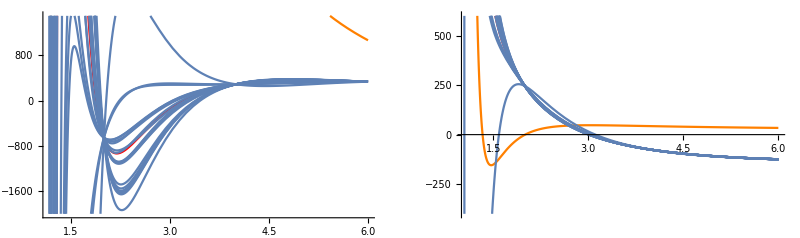

```mathematica
smoothcherryn = gqg3FittedCross[[Position[gqg3invfull, #]& /@ gqg3cherry //Flatten]] /. largeNrules // Simplify;
gqg3Nasy = gqg3N0asy + gqg3N1asyExtened + gqg3Ninf;
g1 = PlotListN[gqg3Nasy, smoothcherryn, 1, -2000, 1500];
g2 = PlotListN[gqg3Nasy, smoothcherryn, 2, -400, 600];
GraphicsRow[{Show[g1, PlotRange-> All],Show[g2, PlotRange-> All]}, ImageSize->Full]
```

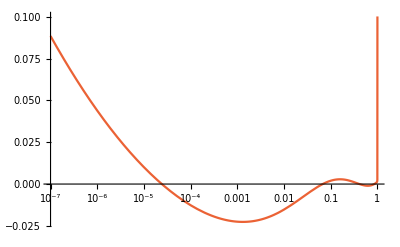
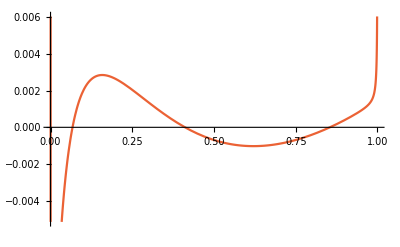
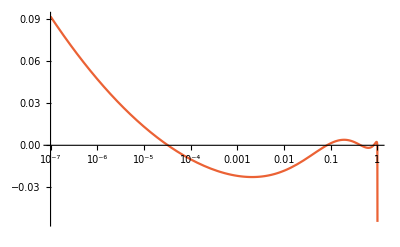
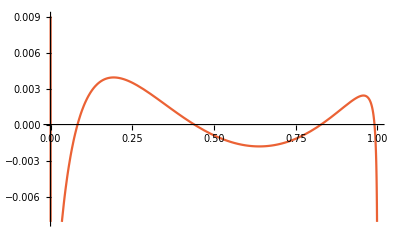
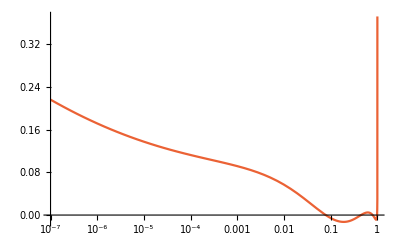
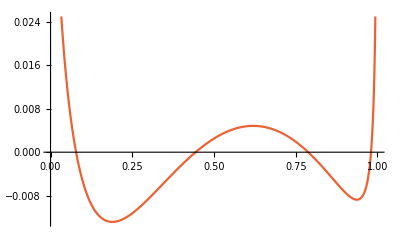
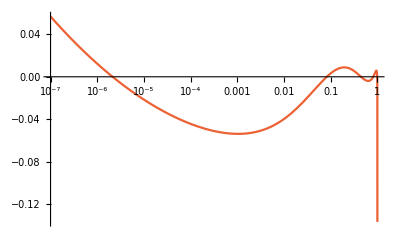
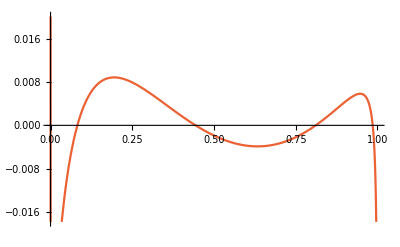
{{1,-Graphics-,-Graphics-},{2,-Graphics-,-Graphics-},{3,-Graphics-,-Graphics-},{4,-Graphics-,-Graphics-},{5,-Graphics-,-Graphics-},{6,-Graphics-,-Graphics-},{7,-Graphics-,-Graphics-},{8,-Graphics-,-Graphics-},{9,-Graphics-,-Graphics-},{10,-Graphics-,-Graphics-},{11,-Graphics-,-Graphics-},{12,-Graphics-,-Graphics-},{13,-Graphics-,-Graphics-},{14,-Graphics-,-Graphics-},{15,-Graphics-,-Graphics-},{16,-Graphics-,-Graphics-},{17,-Graphics-,-Graphics-},{18,-Graphics-,-Graphics-},{19,-Graphics-,-Graphics-},{20,-Graphics-,-Graphics-}}

```mathematica
MapThread[{#1,#2, #3}& ,{ Range[1,graphQGcherryrep//Length ],graphQGcherrylogrep, graphQGcherryrep}]
```

To check: 3

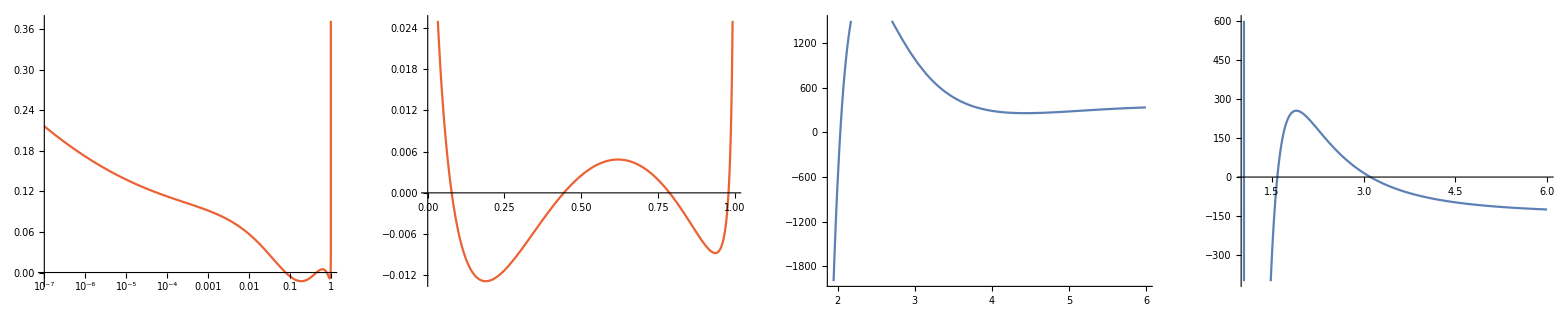

nf ((-1.38788×10^6-19169.9 nf+577.801 nf^2+n (1.38788×10^6+19169.9 nf-577.801 nf^2)+n^3 (73188.5+507.72 nf-52.9542 nf^2)+n^2 (-561325.-5067.53 nf+252.336 nf^2))/((-1.+n) n^3)+(-1258.51-73.3786 nf-0.431678 nf^2) S13m1[n])

```mathematica
posix = 3;
GraphicsRow[{LogPlotList[gqg3cherry, gqg3asy, 4, 4][[posix]], PlotList[gqg3cherry, gqg3asy, 4, 4][[posix]], g1[[posix+1]], g2[[posix+1]]}, ImageSize->Full]
smoothcherryn[[posix]]
```

Remove candidate 3?

```mathematica
(*gqg3cherryrefined = Delete[gqg3cherry, 4];*)
gqg3cherryrefined = gqg3cherry;
graphQGcherrylogrepref = LogPlotList[gqg3cherryrefined, gqg3asy, 4, 4];
graphQGcherryrepref = PlotList[gqg3cherryrefined, gqg3asy, 4, 4];
GraphicsRow[{Show[graphQGcherrylogrepref], Show[graphQGcherryrepref]}]
```

-Graphics-

```mathematica
{graphQGcherry1, graphQGcherrylog1} = PlotErrorBand[gqg3asy, gqg3cherryrefined, 4, 4]; 
legend = {"cross candidate", "cherries"};
GraphicsRow[{
    	ShowLegends[{graphQGlog, graphQGcherrylog1}, LogLinearPlot, legend, {3, 4}], 
    	ShowLegends[{graphQG, graphQGcherry1}, Plot, legend, {3, 4}]
    	}, ImageSize -> Full
 ]
```

-Graphics-

```mathematica
smoothcherryn = gqg3FittedCross[[Position[gqg3invfull, #]& /@ gqg3cherry //Flatten]] /. largeNrules // Simplify;
(* smoothcherryn = Delete[smoothcherryn, 1];*)
gqg3Nasy = gqg3N0asy + gqg3N1asyExtened + gqg3Ninf;
g1ref = PlotListN[gqg3Nasy, smoothcherryn, 1, -2000, 1500];
g2ref = PlotListN[gqg3Nasy, smoothcherryn, 2, -400, 600];
GraphicsRow[{Show[g1ref, PlotRange-> All],Show[g2ref, PlotRange-> All]}, ImageSize->Full]


exportMeList[gqg3Nasy, smoothcherryn, StringJoin[storepath, "gqg3nf1.c"], 1];
exportMeList[gqg3Nasy, smoothcherryn, StringJoin[storepath, "gqg3nf2.c"], 2];
```

-Graphics-

writing to /Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/parametrised_ad/gqg3nf1.c

writing to /Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/parametrised_ad/gqg3nf2.c

```mathematica
smoothcherryn//Length
```

20

### Fitting 10 moments

#### All - x parametrization

Conversion of the  all - x parametrization given in https://arxiv.org/src/2307.04158v1/anc/xPqg3a.f

```mathematica
newgqgmoments = {gqg3N2,gqg3N4,gqg3N6,gqg3N8,gqg3N10,gqg3N12,gqg3N14,gqg3N16,gqg3N18,gqg3N20};
(* In the new paper the large-x limit contains some more terms ... *)
newgqg3Ninf =  gqg3Ninf + nf (+40.511391 -5.5418381 nf-0.16460905 nf^2) Lm14m1[n] -2.8806584 nf Lm15m1[n] -0.8230452700000002 nf^2 Lm15m1[n];
newgqgNasy = gqg3N0asy + gqg3N1asy + newgqg3Ninf;
MellinPqg[NF_, imod_] := Module[{gqg3N, const},
	const = Coefficient[gqg3X[x, NF, imod] /. Log[__] -> 0 /. (1-x) ->0, x, 0];
	gqg3N = (gqg3X[x, NF, imod] - const) /. FastMellin;
	gqg3N = gqg3N + const 1/n;
	- gqg3N
]

gqgNasy = MellinPqg[nf, "asy"] //Expand
```

0.-(7871.52 nf)/(-1+n)^3+(14103.7 nf)/n^7+(2588.84 nf)/n^6+(68802.3 nf)/n^5-(1991.11 nf^2)/n^7+(2069.33 nf^2)/n^6-(7229.38 nf^2)/n^5-(99.1605 nf^3)/n^5-35.6878 nf Lm14[n]+3.51166 nf^2 Lm14[n]+0.0823045 nf^3 Lm14[n]+40.5114 nf Lm14m1[n]-5.54184 nf^2 Lm14m1[n]-0.164609 nf^3 Lm14m1[n]-1.85185 nf Lm15[n]+0.411523 nf^2 Lm15[n]-2.88066 nf Lm15m1[n]-0.823045 nf^2 Lm15m1[n]

Test the asymptotic limit is the same

```mathematica
gqgNasy -(newgqgNasy //. QCDConstantsRules) // Simplify // N
```

0.+(0.0000542039 nf)/(-1.+n)^3-(0.000263704 nf)/n^7+(0.0000538272 nf)/n^6+(0.000771585 nf)/n^5-(8.88889×10^-7 nf^2)/n^7-(0.0000533333 nf^2)/n^6-(0.0000865598 nf^2)/n^5+(1.02716×10^-6 nf^3)/n^5+nf (4.45311×10^-7-7.9561×10^-9 nf+2.51029×10^-10 nf^2) Lm14[n]+(-4.81481×10^-8-3.74486×10^-9 nf) nf Lm15[n]+1.11022×10^-16 nf^2 Lm15m1[n]

```mathematica
NF = 3;
vA = MellinPqg[NF, 1];
vB = MellinPqg[NF, 2];
MapThread[(vA  /. n -> #1) - #2 //. QCDConstantsRules /. ZetaRules  /. nf -> NF &, {Range[2,20,2], newgqgmoments}] //N
MapThread[(vB  /. n -> #1) - #2 //. QCDConstantsRules /. ZetaRules  /. nf -> NF &, {Range[2,20,2], newgqgmoments}] //N
MapThread[((vB + vA)/2 /. n -> #1) - #2 //. QCDConstantsRules /. ZetaRules  /. nf -> NF &, {Range[2,20,2], newgqgmoments}] //N
```

{-0.0876382,-0.023836,-0.0268359,-0.029648,-0.0312146,-0.0319971,-0.032317,-0.0323601,-0.0322342,-0.0320038}

{0.159753,-0.011512,-0.0142082,-0.0132385,-0.0133456,-0.0141007,-0.015102,-0.0161465,-0.0171428,-0.0180544}

{0.0360572,-0.017674,-0.020522,-0.0214432,-0.0222801,-0.0230489,-0.0237095,-0.0242533,-0.0246885,-0.0250291}

#### Fitting 10 moments

```mathematica
momentslist = MapThread[{#1, #2}&, {Range[2,20,2], newgqgmoments}];
flargeN = {
	{1/n^4, 1/n^3, 1/n^2, 1/n,SuppLog[n],Lm13[n], Lm12[n]}, 
	{1/n^4, 1/n^3, 1/n^2, 1/n,SuppLog[n],Lm13[n], Lm12[n]}, 
	{1/n^4, 1/n^3, 1/n^2, 1/n,SuppLog[n],Lm13[n], Lm12[n]}
};
fsmallN = {1/(-1+n)^2, 1/(-1+n)^2, 1/(-1+n)^2};
fSubLeading = {
   	{(S[1,n]-n (π^2/6-S[2,n]))/n^2,(S[1,n]-n (π^2/6-S[2,n]))/n^2,(S[1,n]-n (π^2/6-S[2,n]))/n^2}, (* Log[1-x] Log[x] *)
	  (* {(3+n)/(2+3 n+n^2),(3+n)/(2+3 n+n^2), (3+n)/(2+3 n+n^2)}, (* (2-x) x *)*)
	  {Lm11[n],Lm11[n],Lm11[n]}, (* Log[1-x] *)
	  {Lm13m1[n],Lm13m1[n],Lm13m1[n]}, (* Log[1-x]^3(1-x) *)
	  {Lm12m1[n],Lm12m1[n],Lm12m1[n]}, (* Log[1-x]^2(1-x) *)
	  {Lm11m1[n],Lm11m1[n],Lm11m1[n]},
	  {1/(n+1),1/(n+1),1/(n+1)}
	(* {1/(n+2),1/(n+2),1/(n+2)}*)
	(* {1/(n+1)^2,1/(n+1)^2,1/(n+1)^2}, 
	{1/(n+1)^3,1/(n+1)^3,1/(n+1)^3},
	{S12m1[n],S12m1[n],S12m1[n]},
	{S[1,n-2]/n,S[1,n-2]/n,S[1,n-2]/n}*)
};
newgqg3Fitted = DoAllFits[fsmallN, flargeN, fSubLeading, momentslist, gqg3N0asy, gqg3N1asy, newgqg3Ninf];
newgqg3Fitted //Length
```

15

```mathematica
MapThread[(Mean[newgqg3Fitted] + newgqgNasy /. n -> #1) - #2 //. QCDConstantsRules /. ZetaRules /. nf -> 3 &, {Range[2, 20, 2], newgqgmoments}] // N
```

{-2.45564×10^-11,2.22826×10^-11,-1.697×10^-9,2.65822×10^-8,-1.73588×10^-7,5.76521×10^-7,-1.06081×10^-6,1.09634×10^-6,-5.96271×10^-7,1.32876×10^-7}

#### Test with Vogt

```mathematica
(*Drop this candidate which contain a double term Lm1^2 like...*)
(*newgqg3Fitted[[-1]]
newgqg3Fittedclean = Delete[newgqg3Fitted, -1];
newgqg3Fittedclean // Length*)
```

nf (48247.9/(-1+n)^2+60212.7/n^4+107033./n^3+133204./n^2+1303.33/n+1518.3 Lm12[n]-9088.7 Lm12m1[n]+225.644 Lm13[n]-4064.56 Lm13m1[n]-189718. SuppLog[n])+nf^3 (-11.9264/(-1+n)^2-75.9494/n^4-47.7846/n^3-130.72/n^2+4.20439/n+1.35592 Lm12[n]-32.2603 Lm12m1[n]+1.24742 Lm13[n]-0.445797 Lm13m1[n]+127.553 SuppLog[n])+nf^2 (214.593/(-1+n)^2+4886.41/n^4-5378.09/n^3+886.488/n^2-145.576/n-383.545 Lm12[n]+2591.66 Lm12m1[n]-38.8508 Lm13[n]+396.633 Lm13m1[n]+1086.87 SuppLog[n])

9

```mathematica
mygqg3Xfitted = - MapThread[MellinInverseSinglet[#] &, {newgqg3Fitted}];
mygqg3Xasy = - MellinInverseSinglet[newgqgNasy /. QCDConstantsRules /.ZetaRules];

NF = 4;
my = MapThread[pifact # /. nf -> NF &, {mygqg3Xfitted}];
varA = pifact (gqg3X[x, NF, 1] -  gqg3X[x, NF, "asy"]);
varB = pifact (gqg3X[x, NF, 2] -  gqg3X[x, NF, "asy"]);
avg = Mean[{varA, varB}];
```

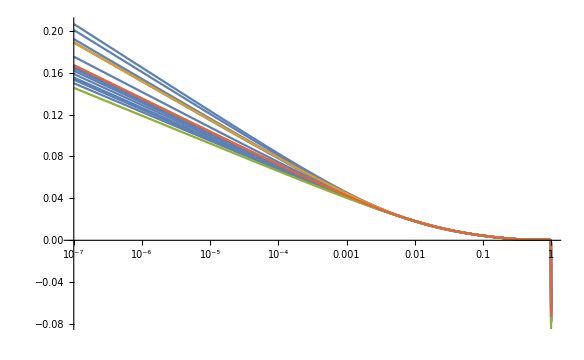

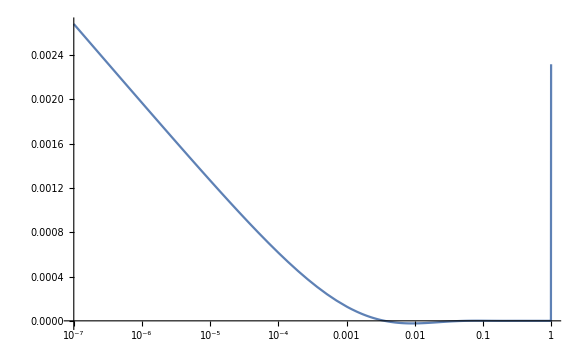

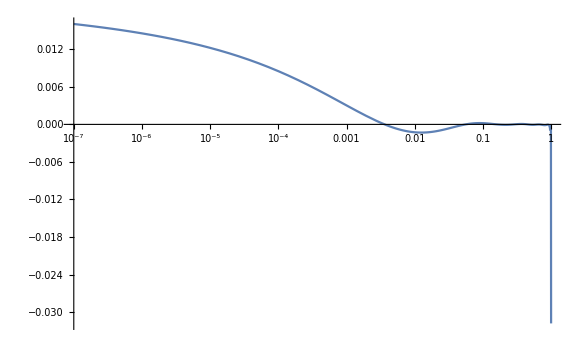

```mathematica
(* Small x *)
p1 = LogLinearPlot[my 1, {x, 10^-7, 1}];
p2 = LogLinearPlot[{varA, varB, avg},
  {x, 10^-7, 1}, PlotStyle -> {clist[[2]], clist[[3]], clist[[4]]}];
Show[{p1, p2}]
LogLinearPlot[Mean[my]-avg, {x, 10^-7, 1}]
LogLinearPlot[(Mean[my]-avg)/avg , {x, 10^-7, 1}]
```

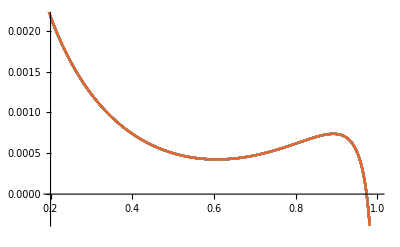

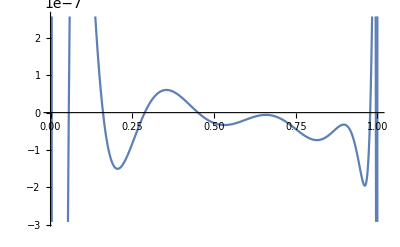

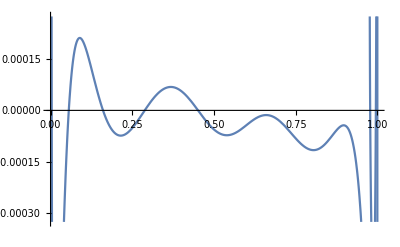

```mathematica
(* Mid x *)
p1 = Plot[ my 1, {x, 0.2, 1}];
p2 = Plot[{varA, varB, avg},{x, 0, 1}, PlotStyle -> {clist[[2]], clist[[3]], clist[[4]]}];
Show[{p1, p2}]
Plot[Mean[my] - avg , {x, 0, 1}]
Plot[(Mean[my]- avg)/avg , {x, 0, 1}]
```

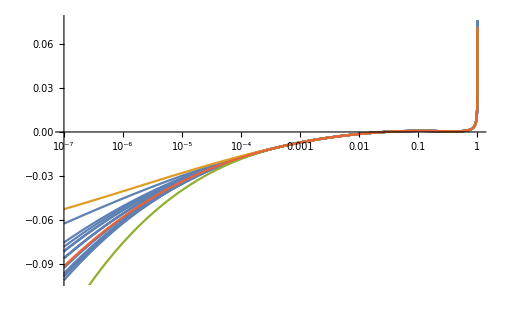

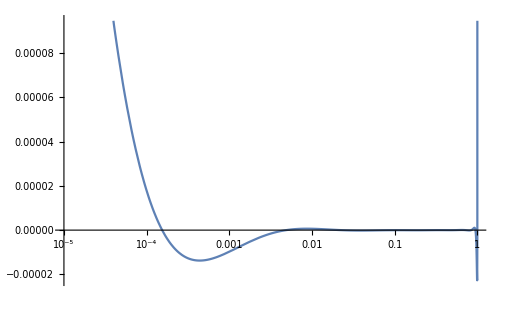

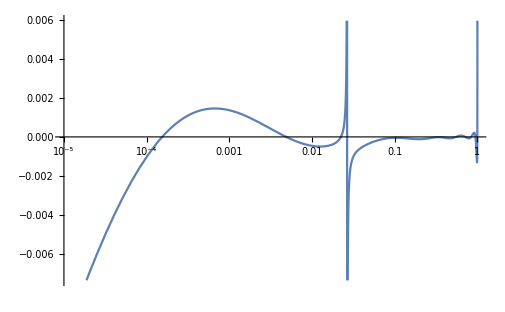

```mathematica
(* Large x *)
p1 = LogLinearPlot[my 1 /. x -> 1 - y, {y, 10^-7, 1}];
p2 = LogLinearPlot[{varA /. x -> 1-y, varB/. x -> 1-y, avg /. x -> 1-y},
 {y, 10^-7, 1}, PlotStyle -> {clist[[2]], clist[[3]], clist[[4]]}];
Show[{p1, p2}]
LogLinearPlot[Mean[my]-avg /. x -> 1-y, {y, 10^-5, 1}]
LogLinearPlot[(Mean[my]-avg)/avg /. x -> 1-y, {y, 10^-5, 1}]
```

```mathematica
{graphQG10mom, graphQG10momlog} = PlotErrorBand[- mygqg3Xasy, - mygqg3Xfitted, 5, 3]; 
{graphQGvogt, graphQGvogtlog} = PlotErrorBand[0, -{gqg3X[x, 5, 1], gqg3X[x, 5, 2]}, 5, 1]; 
legend = {"Vogt", "10 moments"};
GraphicsRow[{
    	ShowLegends[{graphQGvogtlog, graphQG10momlog}, LogLinearPlot, legend, {1,3}], 
    	ShowLegends[{graphQGvogt, graphQG10mom}, Plot, legend, {1, 3}]
    	}, ImageSize -> Full
 ]
```

-Graphics-

Spread with the full set of variations, it looks Vogt errors are estimated correctly ...

-Graphics-

#### Test with 4 moments only

```mathematica
{graphQG10mom, graphQG10momlog} = PlotErrorBand[- mygqg3Xasy, - mygqg3Xfitted, 4, 3]; 
legend = {"4 moments", "10 moments"}; 
GraphicsRow[{
    	ShowLegends[{graphQGcherrylog, graphQG10momlog}, LogLinearPlot, legend, {4,3}], 
    	ShowLegends[{graphQGcherry, graphQG10mom}, Plot, legend, {4, 3}]
    	}, ImageSize -> Full
 ]
```

-Graphics-

```mathematica
gqg3asy3 = Coefficient[mygqg3Xasy, nf, 3];
gqg3nf3x = gqg3nf3x /. QCDConstantsRules //N;
```

```mathematica
graphQGExa3 = Plot[pifact gqg3nf3x, {x, 0, 1}, PlotStyle -> clist[[4]], ImageSize->Full];
graphQGExa3log = LogLinearPlot[ pifact gqg3nf3x, {x, 10^-7, 1}, PlotStyle -> clist[[4]], ImageSize->Full];
```

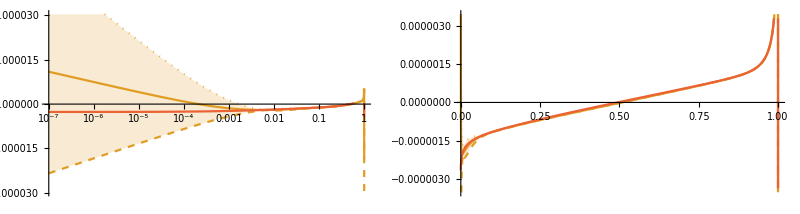

```mathematica
{graphQG3, graphQG3log} = PlotErrorBand[- gqg3asy3, -Coefficient[mygqg3Xfitted, nf,3], 4,2];
GraphicsRow[{
	Show[graphQG3log, graphQGExa3log], 
	Show[graphQG3, graphQGExa3]
	}, ImageSize -> Full
]
```

#### Save

```mathematica
exportMeList[newgqgNasy, newgqg3Fitted, StringJoin[storepath, "gqg3nf1.c"], 1];
exportMeList[newgqgNasy, newgqg3Fitted, StringJoin[storepath, "gqg3nf2.c"], 2];
```

writing to /Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/parametrised_ad/gqg3nf1.c

writing to /Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/parametrised_ad/gqg3nf2.c

#### Test

Here we test that FasMellin is doing the job.

```mathematica
Integrate[-x gqg3X[x, 3, 0], {x, 0, 1}]  
MellinPqg[3, 0]  /. n -> 2 // N
Integrate[-x gqg3X[x, 4, 0], {x, 0, 1}]  
MellinPqg[4, 0]  /. n -> 2 // N
Integrate[-x gqg3X[x, 5, 0], {x, 0, 1}]  
MellinPqg[5, 0]  /. n -> 2 // N
```

221.269

221.269

1251.69

1251.69

2750.83

2750.83

```mathematica
xtest = 0.000000123;
gqg3X[x, 3, 0] /. x -> xtest
MellinInverseSinglet[-MellinPqg[3, 0]] /. x -> xtest
gqg3X[x, 4, 0] /. x -> xtest
MellinInverseSinglet[-MellinPqg[4, 0]] /. x -> xtest
gqg3X[x, 5, 0] /. x -> xtest
MellinInverseSinglet[-MellinPqg[5, 0]] /. x -> xtest
```

8.77011×10^12

8.77011×10^12

1.15942×10^13

1.15942×10^13

1.43648×10^13

1.43648×10^13